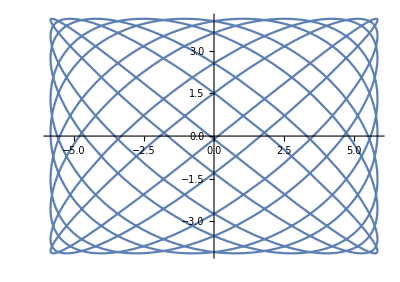

```mathematica
ParametricPlot[{-5*Sin[9*t]+3*Cos[9*t],1*Sin[10*t]-4*Cos[10*t]},{t,0,2Pi}]
```

```mathematica
Manipulate[
ParametricPlot[{A*Cos[a*t+k*π],B*Cos[b*t]},{t,0,2Pi},AspectRatio->Automatic],{{A,1},-2,2},{{B,1},-2,2},{a,1,10},{b,1,10},{k,0,2}]
```

```mathematica
Animate[
ParametricPlot[{Cos[3k*t],Cos[3t]},{t,0,2Pi},AspectRatio->Full],{k,0,1, 0.01},DefaultDuration->15,
AnimationRunning-> False]
```

```mathematica
Animate[
ParametricPlot[{Cos[a*t+π/2],Cos[(a+1)*t+π/2]},{t,0,2Pi},AspectRatio->Automatic],{a,0,15, 0.05},DefaultDuration->45,
AnimationRunning-> False]
```

```mathematica
Manipulate[
ParametricPlot[{A1*Cos[a*t+k1*π]+A2*Sin[a*t+k2*π],B1*Cos[b*t+k3*π]+B2*Sin[b*t+k4*π]},{t,0,2Pi},AspectRatio->Automatic],{{A1,1},-2,2},{{A2,1},-2,2},{{B1,1},-2,2},{{B2,1},-2,2},{{a,4},1,10},{{b,5},1,10},{k1,0,2},{k2,0,2},{k3,0,2},{k4,0,2}]
```

```mathematica
Manipulate[
ParametricPlot[{A1*Sin[a*t+k1*π],B1*Sin[b*t+k2*π]},{t,0,2Pi},AspectRatio->Automatic],
{{A1,1},-2,2},{{B1,1},-2,2},{{a,8},1,10},{{b,9},1,10},{k1,0,2},{k2,0,2}]
```